```mathematica
Clear[m,n]
```

```mathematica
$Assumptions={m,n}∈PositiveIntegers;
```

### Experiment

```mathematica
f[{p_,o_}]:=dis[[p,o]];
Life[alloc_]:=Total[f/@alloc];
Wait[w_, p_,alloc_]:=Total[w[[Complement[p,alloc[[All,1]]]]]];
Goal[w_, p_,alloc_]:=Wait[w, p,alloc]+Life[alloc];
```

```mathematica
RandomSim[p0_, o0_, dis0_, w0_, m0_, n0_]:= Module[{p=p0, w=w0, m=m0, n=n0, o=o0, dis=dis0},
RandomAlloc[w_, p_,o_]:=MapIndexed[If[#2[[1]]<=w[[#1[[1]]]]&&f[#1]>w[[#2[[1]]]],#1,Nothing]&,{RandomSample[p][[;;Min[m,n]]],RandomSample[o][[;;Min[m,n]]]}ᵀ];
SampleGoal[w_, p_,o_]:={Goal[w, p,#], #}&@RandomAlloc[w, p,o];
smps=Table[{#[[1]]/n, #[[2]]}& @SampleGoal[w, p,o],(m+n)^2];
scores = #[[1]]&/@smps;
allocations = #[[2]] &/@smps;
{scores, allocations}
]
```

```mathematica
OptimalSim[p0_, o0_, dis0_, w0_, m0_, n0_]:= Module[{p=p0, w=w0, m=m0, n=n0, o=o0, dis=dis0},
T = Min[m, n];
var[i_,j_, t_] := Symbol["x"<>ToString@i<>"d" <>ToString@j <> "d" <> ToString@t];
waitConstr[w_, i_] :=  Table[Symbol["x"<>ToString@i<>"d" <>ToString@j <> "d" <> ToString@t] == 0, {j, m}, {t, w+1, T}] // Flatten;
EvaluateSolution[alloc_]:= (Total[dis[[#[[1]],#[[2]]]] & /@alloc] + (w[[Complement[p, #[[1]] &/@alloc]]] // Total))/n;
obj1 = Table[-dis[[i,j]]*var[i,j,t], {i,  n}, {j,  m}, {t, T}] // Flatten // Total;
obj2 = Table[-w[[i]] * (1 - (Table[var[i,j,t], {j, m},{t, T}] // Flatten // Total )), {i, n}]  // Total;
obj = obj1 + obj2;
constr = Table[(Flatten[Table[var[i,j,t], {j, m},{t, T}] ] // Total) <= 1, {i, n}];
constr2 = Table[( Flatten[Table[var[i,j,t], {i, n}, {t, T}]] //Total) <= 1, {j, m}];
constr3 = Table[ (Flatten[Table[var[i,j,t], {i, n}, {j, m}]] //Total)<= 1, {t, T}];
constr4 = Table[var[i,j,t] >= 0, {i, n}, {j, m}, {t, T}] // Flatten;
constr5 = waitConstr[#[[1]], #[[2]]]&/@Transpose[{w, p}] // Flatten;
res = LinearOptimization[obj1+obj2, constr~Join~constr2~Join~constr3~Join~constr4~Join~constr5, Table[var[i,j,t]∈ Integers, {i, n}, {j, m}, {t, T}]//Flatten];
SplitRes[s_]:= ToString@s// StringSplit[#, "x"]& // StringSplit[#, "d"]& //ToExpression// Flatten;
ExtractAllocation[res_]:=SortBy[SplitRes[#[[1]]] & /@ Select[res, (#[[2]] == 1&)], Last];
alloc = ExtractAllocation[res];
{EvaluateSolution[alloc], alloc}
];


GreedySim[p0_, o0_, dis0_, w0_, m0_, n0_]:= Module[{p=p0, w=w0, m=m0, n=n0, o=o0, dis=dis0},
λ=Ceiling[m/2]+1;
alc=ConstantArray[0,Min[m,n]];
{pRm,oRm}={Range[n],Range[m]};
{patients,organs}={Table[Subscript[pt, i],{i,n}],Table[Subscript[or, i],{i,m}]};
NormalEdgeForm[ed_]:=(ed/.{Subscript[_, i_]->i})/.DirectedEdge->List;
Zero[a_,b_]:=ConstantArray[Infinity,{a,b}];
FindPosition[alloc_,last_]:=Flatten[Position[alloc[[;;Min[last,Length[alloc]]]],0]];
PlaceAtLast[item_, list_, last_]:=
Module[{l},
l=FindPosition[list,last];
If[Length[l]==0,Return[list]];
Return[ReplacePart[list,Last[l]->item]]
];
While[(Length[oRm]>0)&&(Length[pRm]>0),
adj=Transpose[Join[(Join[ConstantArray[∞,Length[oRm]],#1]&)/@Transpose[dis[[pRm,oRm]]],Zero[Length[pRm],Length[oRm]+Length[pRm]]]/.{0.->∞}];g=WeightedAdjacencyGraph[Join[organs[[oRm]],patients[[pRm]]],adj];
If[Length[g//EdgeList]==0,Break[];Print["Breaking"];];
mm=NormalEdgeForm/@FindMaximumFlow[g,patients[[pRm]],organs[[oRm]],"EdgeList",VertexCapacity->ConstantArray[1,Length[oRm]+Length[pRm]]];wait=w⟦mm⟦All,1⟧⟧;gains=f/@mm-wait;next=Ordering[gains,-1][[1]];
alc=PlaceAtLast[mm[[next]],alc,w[[next]]];
oRm=oRm/.{mm[[next]][[2]]->Nothing};
pRm=pRm/.{mm[[next]][[1]]->Nothing};
];
greedy=Goal[w, p, alc/.{0->Nothing}];
greedy / n
];


Sim[n0_, m0_]:= Module[{n=n0, m=m0},
p=Range[n];
o=Range[m];
w=RandomVariate[PoissonDistribution[15],n];
pZ=RandomVariate[NormalDistribution[0,10],n];
oZ=RandomVariate[NormalDistribution[0,10],m];
dis=5Ramp[DistanceMatrix[pZ,oZ]-5];
randomScores = RandomSim[p, o, dis, w, m, n][[1]];
optimalScore = OptimalSim[p, o, dis, w, m, n][[1]];
greedyScore = GreedySim[p, o, dis, w, m, n];
{Max[randomScores], greedyScore, optimalScore}
];
```

```mathematica
Sim[5, 5]
```

{63.809,46.9488,63.809}

```mathematica
ratios = Table[Table[{#[[3]] / #[[1]], #[[3]]/ #[[2]]}&@Sim[n,n], 10]//Mean, {n,5, 50, 5}]
```

{{1.,1.35651},{1.02041,1.26446},{1.07823,1.29928},{1.19118,1.26818},{1.28278,1.27765},{1.3945,1.2233},{1.4835,1.25218},{1.59684,1.2565},{1.65378,1.19913},{1.66016,1.2571}}

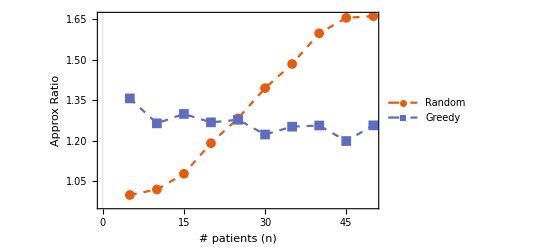

```mathematica
ListLinePlot[{Transpose[{Range[5, 50, 5], #[[1]]&/@ratios}], Transpose[{Range[5, 50, 5], #[[2]]&/@ratios}]},Ticks->{Transpose[{Range[10],Range[5, 50, 5]}], Automatic}, Frame->True,FrameLabel->{"# patients (n)","Approx Ratio"},LabelStyle->{FontSize->18,FontColor->Black,FontFamily->"CMU Sans Serif"},PlotTheme->"Scientific",PlotMarkers->{Automatic, 10},PlotStyle->Dashed, PlotLegends->Placed[{"Random", "Greedy"}, {.25, .8}]]
```

```mathematica
p=Range[30];
o=Range[20];
w=RandomVariate[PoissonDistribution[15],30];
pZ=RandomVariate[NormalDistribution[0,10],30];
oZ=RandomVariate[NormalDistribution[0,10],20];
dis=5Ramp[DistanceMatrix[pZ,oZ]-5];
randomSim = RandomSim[p, o, dis, w, 30, 20];
```

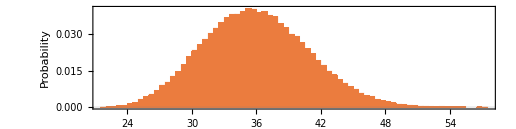

```mathematica
Histogram[randomSim[[1]],50,"Probability",Frame->True,FrameLabel->{"Life Expectancy per Patient","Probability"},LabelStyle->{FontSize->18,FontColor->Black,FontFamily->"CMU Sans Serif"},PlotTheme->"Scientific",AspectRatio->1/4]
```

```mathematica
optimalSim = (*OptimalSim[p, o, dis, w, 30, 20]*)
```